Figure (linearPolarizationFig1.eps) showing the electric and magnetic field directions for a linearly polarized field propagating at a fixed angle to the horizontal in the transverse plane.

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

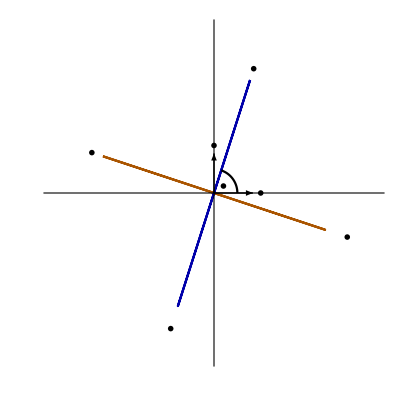

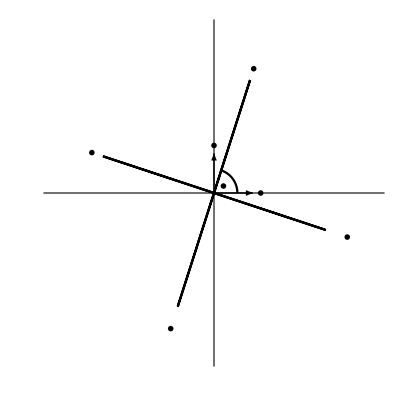

```mathematica
ClearAll[p1, bold, boldsubx, subx, te, pt, f]
pt[r_, t_] := r{Cos[t],Sin[t]};
bold = MaTeX[ "\\mathbf{"<>#<>"}"] &;
boldsubx[x_, i_, s_ : "_"] := (MaTeX[ "\\mathbf{" <> x <>"}" <>s <> ToString[i]] ) ;
subx[x_, i_, s_ : "_"] := (MaTeX[ x <>"" <>s <> ToString[i]] ) ;
te[n_] := boldsubx["e", n];


f[c1_, lc1_, c2_, lc2_]:= Module[{e1,e2, psi, r,o, vecE, te1, te2, vecH, rho},
{e1,e2} = IdentityMatrix[2];
psi = .4 Pi;
rho = 3;
r = rho{-1.4,1.4};
o = {0,0};
vecE = pt[rho,psi] ;
vecH = pt[rho,psi + Pi/2];
te1 = te[ 1];
te2 = te[ 2];
Show[{
ParametricPlot[vecH Cos[ t ], {t, 0, 2 Pi}, 
PlotRange -> {r,r},
Ticks -> None,
PlotStyle-> {c1}
],
ParametricPlot[vecE Cos[ t ], {t, 0, 2 Pi}, 
PlotRange -> {r,r},
Ticks -> None,
PlotStyle-> {c2}
],
ParametricPlot[(rho/5){Cos[t],Sin[t]},{t,0,psi}, PlotStyle-> Black],
Graphics[{
Arrow[{o, e1}],
Arrow[{o, e2}],
Text[te1, 1.2 e1],
Text[te2, 1.2 e2],
Text[MaTeX[ lc2<>"\\mathbf{e}_1 E e^{i\\phi}"], 1.1 vecE],
Text[MaTeX[lc2<>"-\\mathbf{e}_1 E e^{i\\phi}"], -1.2 vecE],
Text[MaTeX[lc1<>"\\mathbf{e}_2 \\frac{E}{\\eta} e^{i\\phi}"], 1.1 vecH],
Text[MaTeX[lc1<>"-\\mathbf{e}_2 \\frac{E}{\\eta} e^{i\\phi}"], -1.2 vecH],
Text[ "\\phi" // MaTeX, pt[0.3,psi/2]]
},
AspectRatio-> 1 ]
}]
]

linearPolarizationFig1 = f[Orange//Darker, "\\color{OrangeDarker}", Blue // Darker, "\\color{BlueDarker}"]

bwlinearPolarizationFig1 = f[Black, "", Black, ""]
```

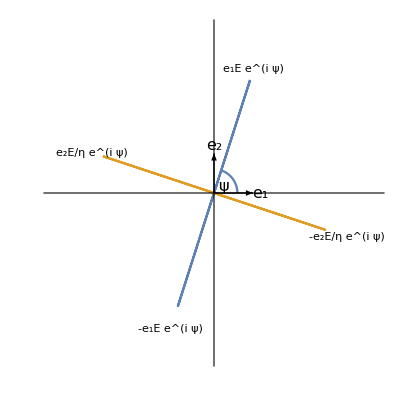

```mathematica
peeters`exportForLatex["color/linearPolarizationFig1", linearPolarizationFig1]
peeters`exportForLatex["bw/linearPolarizationFig1", bwlinearPolarizationFig1]
```

{color/linearPolarizationFig1.eps,color/linearPolarizationFig1pn.png}

{bw/linearPolarizationFig1.eps,bw/linearPolarizationFig1pn.png}